```mathematica
tstart=AbsoluteTime[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["VariationalMethods`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
ClearAll[Sd,γm,γp,q2SolDEL,h,k,m,r,q01,q02,v01,v02,q11,q12,qrecursive,σRK,EL]
```

```mathematica
(*k=0;*)
```

### Definition of the continuous Lagrangian and Rayleigh potential

```mathematica
n=2;
```

```mathematica
Q[t_]:={Q1[t],Q2[t]};
```

```mathematica
q0={q01,q02};
q1={q11,q12};
```

```mathematica
v0={v01,v02};
```

```mathematica
ELeq:=VariationalD[L[Q[t],Q'[t]],Q[t],t]+f[Q[t],Q'[t]]==ConstantArray[0,n]
```

```mathematica
T[v_]:=1/2*v.v
```

```mathematica
V[q_]:=q.q*(q.q-1)^2
```

```mathematica
(*V[q_]:=0*)
```

```mathematica
L[q_,v_]:=T[v]-V[q]
```

```mathematica
EL[q_,v_]:=T[v]+V[q]
```

```mathematica
R[q_,v_]:=1/2*r*Sum[v[[i]]^2,{i,n}]
```

```mathematica
f[q_,v_]=Quiet[Table[-D[R[q,v],v[[i]]],{i,n}]];
```

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
angularmomentum[q_,v_]:=q[[2]]*v[[1]]-q[[1]]*v[[2]]
```

### Midpoint discrete Lagrangians and Rayleigh potential

```mathematica
Ld[q0_,q1_]:=h*L[(q0+q1)/2,(q1-q0)/h]
```

```mathematica
Rd[q0_,q1_]:=h^2/2*R[(q0+q1)/2,(q1-q0)/h]
```

```mathematica
Ldp[q0_,q1_]:=Ld[q0,q1]+Rd[q0,q1]
```

```mathematica
Ldm[q0_,q1_]:=Ld[q0,q1]-Rd[q0,q1]
```

```mathematica
fdp[q0_,q1_]:=h/2*f[(q0+q1)/2,(q1-q0)/h]
```

```mathematica
fdm[q0_,q1_]:=h/2*f[(q0+q1)/2,(q1-q0)/h];
```

```mathematica
fdp[{q01,q02},{q11,q12}]==-Grad[Rd[{q01,q02},{q11,q12}],{q11,q12}]&&fdm[{q01,q02},{q11,q12}]==Grad[Rd[{q01,q02},{q11,q12}],{q01,q02}]//Simplify
```

True

### Discrete Euler-Lagrange equations

```mathematica
h=.2;
```

```mathematica
r=10^(-3);
```

```mathematica
DEL[q01_,q02_,q11_,q12_]=Grad[Ldm[{q01,q02},{q11,q12}],{q11,q12}]+Grad[Ldp[{q11,q12},{q21,q22}],{q11,q12}]==0;
```

```mathematica
solsDEL[q01_,q02_,q11_,q12_]:=NSolve[DEL[q01,q02,q11,q12],{q21,q22},Reals][[1,1;;2,2]]
```

```mathematica
solsDEL[0,0,1,1]
```

{1.36939,1.36939}

### Continuous Euler-Lagrange equations

```mathematica
tend=2000;
```

```mathematica
(*{q01,q02}={1/Sqrt[2],1/Sqrt[2]};*)
```

```mathematica
(*{v01,v02}={Sqrt[(.55)/2],Sqrt[(.55)/2]};*)
```

```mathematica
q01=0;
```

```mathematica
q02=Solve[x^2(x^2-1)^2==.15,x,Reals][[2,1,2]];
```

```mathematica
{v01,v02}={Sqrt[.25],0};
```

```mathematica
EL[{q01,q02},{v01,v02}]==(0.25+0.3)/2
```

True

```mathematica
Rationalize [(0.25+0.3)/2]
```

11/40

```mathematica
ELeq:=VariationalD[L[Q[t],Q'[t]],Q[t],t]+f[Q[t],Q'[t]]=={0,0}
```

```mathematica
(*ELeq*)
```

```mathematica
(*DSolve[ELeq,{Q1[t],Q2[t]},t]*)
```

```mathematica
ClearAll[Q1,Q2,solsEL]
```

```mathematica
solsEL[t_]=NDSolve[{ELeq,Q1[0]==q01,Q2[0]==q02,Q1'[0.0]==v01,Q2'[0.0]==v02},{Q1[t],Q2[t]},{t,0,tend}][[1,1;;2,2]]
```

{InterpolatingFunction[{{0., 2000.}}, <>][t],InterpolatingFunction[{{0., 2000.}}, <>][t]}

Energy

```mathematica
Energy[t_]=EL[solsEL[t],solsEL'[t]]//Simplify;
```

```mathematica
angularmomentumtime[t_]=angularmomentum[solsEL[t],solsEL'[t]]//Simplify;
```

### Runge-Kutta method

```mathematica
RKsols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[{Q1[t],Q2[t]}]],Q1[0]==q01,Q2[0]==q02,Q1'[0.0]==v01,Q2'[0.0]==v02},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4}},StartingStepSize->h]][[-1,1]];
```

```mathematica
RKpts=Table[{h*n,RKsols[[n,1]],RKsols[[n,2]]},{n,1,Floor[tend/h]}];
```

```mathematica
RKpts[[2500]]
```

{500.,-0.371504,-0.948463}

```mathematica
(*Eulersols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[{Q1[t],Q2[t]}]],Q1[0]==q01,Q2[0]==q02,Q1'[0.0]==v01,Q2'[0.0]==v02},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitEuler"}},StartingStepSize->h]][[-1,1]];*)
```

```mathematica
(*Eulerpts=Table[{h*n,Eulersols[[n,1]],Eulersols[[n,2]]},{n,1,Floor[tend/h]}];*)
```

### Continuous vs discrete

```mathematica
{q11,q12}=solsEL[h];
```

```mathematica
qrecursive[0]={q01,q02};
qrecursive[1]= {q11,q12};
qrecursive[n_]:=qrecursive[n]=solsDEL[qrecursive[n-2][[1]],qrecursive[n-2][[2]],qrecursive[n-1][[1]],qrecursive[n-1][[2]]]
```

```mathematica
discretepts=Table[{h*n,qrecursive[n][[1]],qrecursive[n][[2]]},{n,0,Floor[tend/h]}];
```

```mathematica
(*Show[
ParametricPlot3D[{t,solsEL[t][[1]],solsEL[t][[2]]},{t,0,10},PlotLegends->Placed[{"Benchmarck"},Above]],
ListPointPlot3D[Legended[discretepts,Placed["Variational midpoint",Above]],PlotStyle->Red],
(*ListPointPlot3D[Legended[Eulerpts,Placed["Euler method",Above]],PlotStyle->Green],*)
ListPointPlot3D[Legended[RKpts,Placed["Runge-Kutta",Above]],PlotStyle->Green],
AxesLabel->{"t","q.b9(t)","q.b2(t)"},
PlotRange->{{0,10},Automatic,Automatic}
]*)
```

```mathematica
energypts=Table[{h*n,EL[{(discretepts[[n]][[2]]+discretepts[[n-1]][[2]])/2,
(discretepts[[n]][[3]]+discretepts[[n-1]][[3]])/2},{(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])/h,
(discretepts[[n]][[3]]-discretepts[[n-1]][[3]])/h}]},{n,2,Floor[tend/h]}];
```

```mathematica
(*energyRKpts=Table[{h*n,EL[{(RKpts[[n]][[2]]+RKpts[[n-1]][[2]])/2,
(RKpts[[n]][[3]]+RKpts[[n-1]][[3]])/2},{(RKpts[[n]][[2]]-RKpts[[n-1]][[2]])/h,
(RKpts[[n]][[3]]-RKpts[[n-1]][[3]])/h}]},{n,2,Floor[tend/h]}];*)
```

```mathematica
energyRKpts=Table[{h*n,EL[{RKpts[[n]][[2]],
RKpts[[n]][[3]]},{(2(RKpts[[n+1]][[2]]-RKpts[[n-1]][[2]]))/(3h)+(-RKpts[[n+2]][[2]]+RKpts[[n-2]][[2]])/(12h),
(2(RKpts[[n+1]][[3]]-RKpts[[n-1]][[3]]))/(3h)+(-RKpts[[n+2]][[3]]+RKpts[[n-2]][[3]])/(12h)}]},{n,3,Floor[tend/h]}];
```

Part::partw: Part 10001 of {{0.2,0.0987963,1.11202},{0.4,0.193123,1.01034},«47»,{10.,-0.38101,1.07731},«9950»} does not exist.

Part::partw: Part 3 of {{0.2,0.0987963,1.11202},{0.4,0.193123,1.01034},«47»,{10.,-0.38101,1.07731},«9950»}⟦10001⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*energyEulerpts=Table[{h*n,EL[{1/2(Eulerpts[[n]][[2]]+Eulerpts[[n-1]][[2]]),
1/2(Eulerpts[[n]][[3]]+Eulerpts[[n-1]][[3]])},{1/h(Eulerpts[[n]][[2]]-Eulerpts[[n-1]][[2]]),
1/h(Eulerpts[[n]][[3]]-Eulerpts[[n-1]][[3]])}]},{n,2,Floor[tend/h]}];*)
```

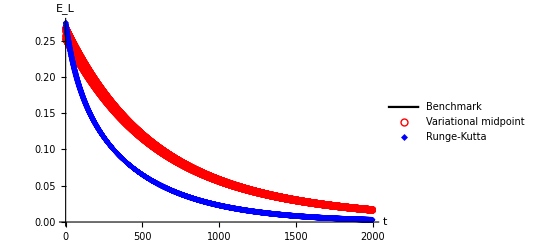

```mathematica
energy=Show[
Plot[Energy[t],{t,0,tend},PlotStyle->Black,PlotLegends->Placed[{"Benchmark"},Above]],ListPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red, PlotMarkers->{"○",Scaled[.005]}],
(*ListPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],*)
ListPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Blue,PlotMarkers->{"◆",Scaled[.005]}],
(*PlotRange->{{0,tend},{0,.3}},*)
 AxesLabel->{"t","E_L"}]
```

```mathematica
Export["./energy_Marsden_West.pdf",energy]
```

./energy_Marsden_West.pdf

```mathematica
(*Plot[Energy[t],{t,0,tend},PlotLegends->Placed[{"True solution"},Above],PlotRange->{{0,tend},{0,1.1}}]*)
```

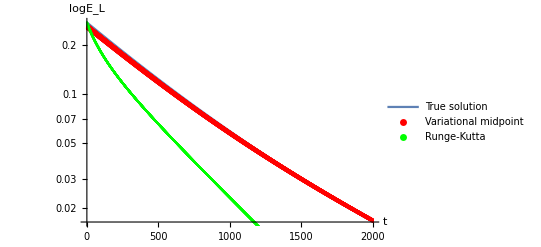

```mathematica
energylog=Show[LogPlot[Energy[t],{t,0,tend},PlotLegends->Placed[{"True solution"},Above]],ListLogPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red],
(*ListLogPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],*)
ListLogPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Green],
(*PlotRange->{{0,tend},Automatic},*)
 AxesLabel->{"t","logE_L"}]
```

```mathematica
angularmomentumpts=Table[{h*n,angularmomentum[{(discretepts[[n]][[2]]+discretepts[[n-1]][[2]])/2,
(discretepts[[n]][[3]]+discretepts[[n-1]][[3]])/2},{(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])/h,
(discretepts[[n]][[3]]-discretepts[[n-1]][[3]])/h}]},{n,2,Floor[tend/h]}];
```

```mathematica
angularmomentumRKpts=Table[{h*n,angularmomentum[{RKpts[[n]][[2]],
RKpts[[n]][[3]]},{(2(RKpts[[n+1]][[2]]-RKpts[[n-1]][[2]]))/(3h)+(-RKpts[[n+2]][[2]]+RKpts[[n-2]][[2]])/(12h),
(2(RKpts[[n+1]][[3]]-RKpts[[n-1]][[3]]))/(3h)+(-RKpts[[n+2]][[3]]+RKpts[[n-2]][[3]])/(12h)}]},{n,3,Floor[tend/h]-2}];
```

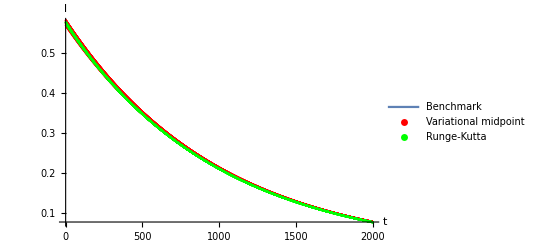

```mathematica
angularmomentumplot=Show[
Plot[angularmomentumtime[t],{t,0,tend},PlotLegends->Placed[{"Benchmark"},Above]],ListPlot[Legended[angularmomentumpts,Placed["Variational midpoint",Above]],PlotStyle->Red],
(*ListPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],*)
ListPlot[Legended[angularmomentumRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Green],
(*PlotRange->{{0,tend},{0,.3}},*)
 AxesLabel->{"t","l"}]
```

```mathematica
(AbsoluteTime[]-tstart)/60
```

2.7176458